## (تمرین ψ=A*sin^4((π*x)/l) (الف

```mathematica
ψ:=A(Sin[(π*x)/l])^4
Solve[∫_0^l ψ^2 ⅆx==1,A]
```

{{A→-(8 √(2/35))/(√l)},{A→(8 √(2/35))/(√l)}}

## (ب

```mathematica
A=√(128/(35l));
t=π;
t0=0;
ℏ=6.62*10^-34;
l=0.5;
m=9.109*10^-31;
En[n_]=(n^2*π^2*ℏ^2)/(2*m*l^2);
Psi[y_]=∑_(n=1)^4 2/l*Exp[(-ⅈ*En[n]*(t-t0))/ℏ]*Sin[(n*π*y)/l]∫_0^l Sin[(n*π*x)/l]*ψⅆx
```

(0.+0. ⅈ)+(1.83465-0.0827398 ⅈ) Sin[6.28319 y]-(0.723216-0.310565 ⅈ) Sin[18.8496 y]

## (ج

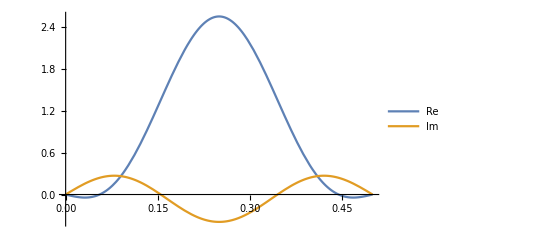

```mathematica
Plot[{Re[Psi[y]],Im[Psi[y]]},{y,0,0.5},PlotStyle->Thick,PlotLegends->{"Re","Im"}]
```

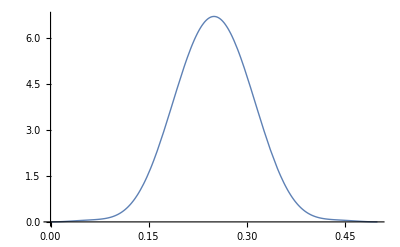

```mathematica
Plot[Psi[y]*Conjugate[Psi[y]],{y,0,0.5},PlotStyle->Thick]
```